### Арифметические операции

#### Задание 1.1.

```mathematica
123+987
12.682+873.119
548-294
446.7321-29.013
35*721
35.0*721
57.29*48.117
21/35
46/13
46.0/13
257.34/868.014
21^35
7.68^12.3
```

1110

885.801

254

417.719

25235

25235.

2756.62

3/5

46/13

3.53846

0.29647

18952884486433699020098042171468383867092598701

7.76145×10^10

#### Задание 1.2

```mathematica
(1/5+3/11)^3-5*(2+4)
25.5/4+(2+4)/3^3
```

-4973674/166375

6.59722

#### Задание 1.3

```mathematica
586/46
N[586/46]
N[586/46, 25]
7^25
N[7^25]
N[7^25, 25]
```

293/23

12.7391

12.73913043478260869565217

1341068619663964900807

1.34107×10^21

1.341068619663964900807×10^21

#### Задание 1.4

```mathematica
389.65/4.7
N[389.65/4.7, 16]
```

82.9043

82.9043

#### Задание 1.5

```mathematica
N[π^3]
N[35!]
N[ⅇ^4.7]
N[Log[ⅇ^8]]
N[Log[3, 6561]]
N[Log[2*π], 30]
```

31.0063

1.03331×10^40

109.947

8.

8.

1.83787706640934548356065947281

#### Задание 1.6

```mathematica
Sin[π/6]
N[Sin[π/6]]
Sin[(13*π)/5]
N[Sin[(13*π)/5]]
Cos[30°]
N[Cos[30°]]
ArcCos[1/2]
N[ArcCos[1/2]]
ArcSin[.4]
N[ArcSin[.4]]
Tan[π/3]
N[Tan[π/3]]
ArcTan[3^(.5)]
N[ArcTan[3^(.5)]]
```

1/2

0.5

√(5/8+(√5)/8)

0.951057

(√3)/2

0.866025

π/3

1.0472

0.411517

0.411517

√3

1.73205

1.0472

1.0472

#### Задание 1.7

```mathematica
√(16)
√(x^2)
√(Abs[x])^2
```

4

√(x^2)

Abs[x]

#### Задание 1.8

```mathematica
?Degree
```

#### Задание 1.9

```mathematica
?*Log*
```

### Операторы присваивания. Подстановки.

#### Задание 2.1

```mathematica
x= RandomReal[]
y:=RandomReal[]
{x, x, x, x, x}
{y, y, y, y, y}
Clear[x,y]
```

0.284716

{0.284716,0.284716,0.284716,0.284716,0.284716}

{0.568734,0.655041,0.42924,0.740435,0.0845683}

#### Задание 2.2

```mathematica
x*ⅇ^x+Log[x]-y/. {x->1, y->2}
x*ⅇ^x+Log[x]-y/. {x->2a, y->b+c}
x^2+y^2+(Sin^2)[x]+(Cos^2)[x]+1.5/.{x->1, y->2}
x^2+y^2+(Sin^2)[x]+(Cos^2)[x]+1.5/. {x->2a, y->b+c}
```

-2+ⅇ

-b-c+2 a ⅇ^(2 a)+Log[2 a]

6.5+Cos^2[1]+Sin^2[1]

1.5+4 a^2+(b+c)^2+Cos^2[2 a]+Sin^2[2 a]

#### Задание 2.3

```mathematica
{x*ⅇ^-x, x^2, Sin[x], 2/(x^2-1)}/.x->{0.3, 0.6, 0.9, 1.2, 1.5, 1.8}
```

{{0.222245,0.329287,0.365913,0.361433,0.334695,0.297538},{0.09,0.36,0.81,1.44,2.25,3.24},{0.29552,0.564642,0.783327,0.932039,0.997495,0.973848},{-2.1978,-3.125,-10.5263,4.54545,1.6,0.892857}}

```mathematica
TableForm[{x, x*ⅇ^-x, x^2, Sin[x], 2/(x^2-1)}/.x->{0.3, 0.6, 0.9, 1.2, 1.5, 1.8}, TableHeadings->{{"x", "x*ⅇ^-x", "x^2", "Sin[x]", "2/x^2"}, None}]
```

x | 0.3 | 0.6 | 0.9 | 1.2 | 1.5 | 1.8
x*ⅇ^-x | 0.222245 | 0.329287 | 0.365913 | 0.361433 | 0.334695 | 0.297538
x^2 | 0.09 | 0.36 | 0.81 | 1.44 | 2.25 | 3.24
Sin[x] | 0.29552 | 0.564642 | 0.783327 | 0.932039 | 0.997495 | 0.973848
2/x^2 | -2.1978 | -3.125 | -10.5263 | 4.54545 | 1.6 | 0.892857

### Преобразование символьных выражений.

#### Задание 3.1

```mathematica
Factor[Expand[(x+1)^4-x^4-2x-1]]
```

2 x (1+x) (1+2 x)

```mathematica
Clear[x, y]
```

#### Задание 3.2

```mathematica
FactorTerms[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z]
FactorTerms[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, x]
```

6 (5 y+x y+2 y^2-5 z-x z-2 y z)

6 (5+x+2 y) (y-z)

#### Задание 3.3

```mathematica
Collect[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, y]
Collect[12*y^2+6*x*y-6*x*z-12*y*z+
30*y-30*z, {y, z}]
Collect[12*y^2+6*x*y-6*x*z-12*y*z+30*y-30*z, {z, y}]
```

12 y^2+y (30+6 x-12 z)-30 z-6 x z

12 y^2+y (30+6 x-12 z)+(-30-6 x) z

(30+6 x) y+12 y^2+(-30-6 x-12 y) z

#### Задание 3.4

```mathematica
Cancel[(2*x^3+x*(5*x-1)-1)/(8*x^3-12*x^2+6*x-1)]
Together[(2x-1)-x2-5
(4x)^2-4*x+1-2*x^3+x*(5 x-1)-1]
Apart[(2*x-1)-(x)^2-5
(4x)^2-4*x+1-2*x^3+x*(5*x-1)-1]
```

(1+3 x+x^2)/(-1+2 x)^2

-1-5  (4x)^2-3 x+5 x^2-2 x^3-x2

-1-5  (4x)^2-(x)^2-3 x+5 x^2-2 x^3

#### Задание 3.5

```mathematica
TrigExpand[Cot[x]-Tan[x]-2 Tan[2*x]]
TrigFactor[Cot[x]-Tan[x]-2*Tan[2*x]]
TrigReduce[Cot[x]-Tan[x]-2*Tan[2*x]]
Simplify[Cot[x]-Tan[x]-2*Tan[2*x]]
TrigToExp[Sinh[x]+Cosh[x]]
Simplify[TrigToExp[Cot[x]-Tan[x]-2*Tan[2*x]]]
ExpToTrig[ⅇ^(ι*x)]
Simplify[ExpToTrig[1/16*ⅇ^(-4ιx)(1+ⅇ^(2ιx))^4]
```

(Cos[x]^2 Cot[x])/(Cos[x]^2-Sin[x]^2)-(6 Cos[x] Sin[x])/(Cos[x]^2-Sin[x]^2)+(Sin[x]^2 Tan[x])/(Cos[x]^2-Sin[x]^2)

Csc[π/4-x] Csc[x] Csc[π/4+x] Sec[x] Sin[π/4-2 x] Sin[π/4+2 x]

Cos[4 x] Csc[x] Sec[x] Sec[2 x]

4 Cot[4 x]

ⅇ^x

(4 ⅈ (1+ⅇ^(8 ⅈ x)))/(-1+ⅇ^(8 ⅈ x))

Cosh[x ι]+Sinh[x ι]

#### Задание 3.6

```mathematica
Simplify[(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)]
Simplify[1/8*(Cos[4*x]+4*Cos[2*x]+3)]
```

1+x

Cos[x]^4

#### Задание 3.7

```mathematica
Factor[(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)]
Factor[x^4-6 x^3-4 x^2-18x-21]/(x^3-7 x^2+3x-21)
■(x^4-6 x^3-4 x^2-18x-21)/(x^3-7 x^2+3x-21)
```

1+x

((-7+x) (1+x) (3+x^2))/(-21+3 x-7 x^2+x^3)

((-21-18 x-4 x^2-6 x^3+x^4) ■)/(-21+3 x-7 x^2+x^3)

### Операции математического анализа(ч.1)

#### Задание 4.1

```mathematica
Sum[k!*k, {k, 1, n}]
Sum[a*q^k, {k, 0,Infinity}]
Sum[1/(2k-1)^4, {k, 1, ∞}]
Sum[1/(2^k k), {k, 1, ∞}]
∑_(k=1)^(n-1) Sin[(π*k)/n]
∑_(k=1)^n (k^2+k-1)/((k+2)!)
∑_(k=1)^∞ 1/((2k+1)!)
∑_(k=1)^∞ (2k)/((2k+1)!)
```

-1+(1+n)!

a/(1-q)

π^4/96

Log[2]

Cot[π/(2 n)]

(-6-8 n-2 n^2+(3+n)!)/(2 (3+n)!)

-1+Sinh[1]

1/ⅇ

#### Задание 4.2

```mathematica
Sum[x^(n+2)/(n!),{x, 0, ∞}]
```

∑_(x=0)^∞ x^(2+n)/(n!)

#### Задание 4.3

```mathematica
Product[1+(-1)^(k+1)/(2k-1), {k, 1, ∞}]
Product[1-1/(2k-1)^2, {k, 2, ∞}]
x*∏_(k=1)^∞ (1+x^2/(k^2 π^2))
x*∏_(k=1)^∞ (1-x^2/(k^2 π^2))
```

√2

π/4

Sinh[x]

x Sinc[x]

#### Задание 4.4

```mathematica
Product[(1+x^(2n)), x]
```

#### Задание 4.5

```mathematica
Table[(x^2+1)/x, {x, 1, 5}]
Table[xⅇ^x, {x, 1, 5}]
Table[(x^2+y^2)/(2x), {x, 1, 5}]
```

{2,5/2,10/3,17/4,26/5}

{xⅇ,xⅇ^2,xⅇ^3,xⅇ^4,xⅇ^5}

{1/2 (1+y^2),1/4 (4+y^2),1/6 (9+y^2),1/8 (16+y^2),1/10 (25+y^2)}

#### Задание 4.6

```mathematica
TableForm[Table[{x, x^2, ⅇ^x//N, Log[x]//N}, {x, 1, 10}], TableHeadings->{None, {"x", "x^2", "ⅇ^x", "Log[x]"}}]
```

x | x^2 | ⅇ^x | Log[x]
1 | 1 | 2.71828 | 0.
2 | 4 | 7.38906 | 0.693147
3 | 9 | 20.0855 | 1.09861
4 | 16 | 54.5982 | 1.38629
5 | 25 | 148.413 | 1.60944
6 | 36 | 403.429 | 1.79176
7 | 49 | 1096.63 | 1.94591
8 | 64 | 2980.96 | 2.07944
9 | 81 | 8103.08 | 2.19722
10 | 100 | 22026.5 | 2.30259

#### Задание 4.7

```mathematica
TableForm[Table[{x, x^2, √x}, {x, 5, 9, 0.5}], TableHeadings->{None, {"x", "x^2", "x^(1/2)"}}, TableDirections->Row]
```

x | 5. | 5.5 | 6. | 6.5 | 7. | 7.5 | 8. | 8.5 | 9.
x^2 | 25. | 30.25 | 36. | 42.25 | 49. | 56.25 | 64. | 72.25 | 81.
x^(1/2) | 2.23607 | 2.34521 | 2.44949 | 2.54951 | 2.64575 | 2.73861 | 2.82843 | 2.91548 | 3.

#### Задание 4.8

```mathematica
TableForm[Table[n!m!, {n, 1, 5}, {m, 1, 7}], TableHeadings->{{"n=1", "n=2", "n=3", "n=4", "n=5"}, {"m=1", "m=2", "m=3", "m=4", "m=5", "m=6", "m=7"}}]
```

| m=1 | m=2 | m=3 | m=4 | m=5 | m=6 | m=7
n=1 | 1 | 2 | 6 | 24 | 120 | 720 | 5040
n=2 | 2 | 4 | 12 | 48 | 240 | 1440 | 10080
n=3 | 6 | 12 | 36 | 144 | 720 | 4320 | 30240
n=4 | 24 | 48 | 144 | 576 | 2880 | 17280 | 120960
n=5 | 120 | 240 | 720 | 2880 | 14400 | 86400 | 604800

### Операции математического анализа(ч.2)

#### Задание 5.1

```mathematica
Limit[(1-ⅇ^(-2t))/Log[1-3t], t->0]
Limit[(1-a^n)/(1-ⅇ^n), n->0]
Limit[(1-ⅇ^x)/(1-ⅇ^-x), x->0]
Limit[(1-x)^(1/(1-x)), x->∞]
Limit[(x-a)/Log[x-a+1], x->a]
Limit[(n^2-n^x)/(x-2), x->2]
```

-2/3

Log[a]

-1

1

1

-n^2 Log[n]

#### Задание 5.2

π/2

-π/2

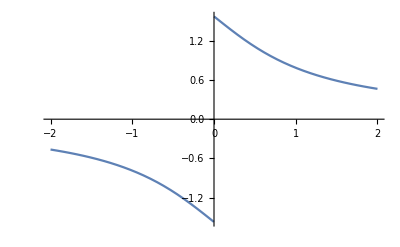

∞

-∞

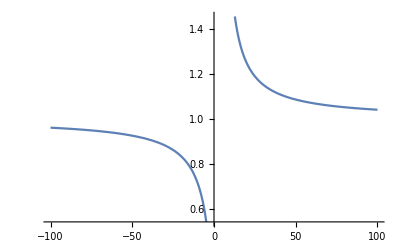

1

1

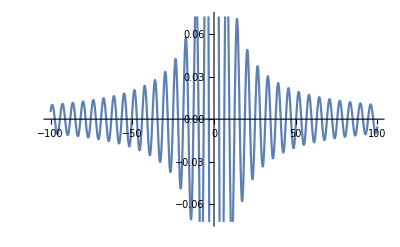

```mathematica
Limit[ArcTan[1/x], x->0, Direction->"FromAbove"]
Limit[ArcTan[1/x], x->0, Direction->"FromBelow"]
Plot[ArcTan[1/x], {x, -2, 2}]
Limit[x/(x-4), x->4, Direction->"FromAbove"]
Limit[x/(x-4), x->4, Direction->"FromBelow"]
Plot[x/(x-4), {x, -100, 100}]
Limit[Sin[x]/Abs[x], x->0,  Direction->"FromAbove"]
Limit[Sin[x]/Abs[x], x->0,  Direction->"FromAbove"]
Plot[Sin[x]/Abs[x], {x, -100, 100}]
```

#### Задание 5.3

```mathematica
Limit[2(a(1-ⅇ^-ax))/(2-ⅇ^-ax),x ->Infinity, Assumptions->a>0]
Limit[2*(a(1-ⅇ^-ax))/(2-ⅇ^-ax), x->Infinity, Assumptions->a<0]
```

(2 a (1-ⅇ^-ax))/(2-ⅇ^-ax)

(2 a (1-ⅇ^-ax))/(2-ⅇ^-ax)

```mathematica
Limit[a^x/x^a, x->Infinity, Assumptions->a>1]
Limit[a^x/x^a, x->Infinity, Assumptions->a≥0 && a ≤1]
```

∞

ConditionalExpression[0,Log[a]<0]

#### Задание 5.4

```mathematica
Series[f[x], {x, 0, 2}]
Series[f[x], {x, a, 2}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+O[x]^3

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+O[x-a]^3

#### Задание 5.5

```mathematica
Series[Sin[x]/Cos[x],{x, 0, 6}]
Series[Sinh[x]*Cosh[x], {x, 0, 6}]
Series[Log[x], {x, 0, 4}]
Collect[Series[Log[x], {x, 1, 4}], x]
```

x+x^3/3+(2 x^5)/15+O[x]^7

x+(2 x^3)/3+(2 x^5)/15+O[x]^7

Log[x]+O[x]^5

-25/12+4 x-3 x^2+(4 x^3)/3-x^4/4

#### Задание 5.6

```mathematica
Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}]
Normal[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}]]
Collect[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}], x]
Collect[Series[Exp[y]*Sin[x], {x, 0, 5}, {y, 0, 3}], y]
```

(1+y+y^2/2+y^3/6+O[y]^4) x+(-1/6-y/6-y^2/12-y^3/36+O[y]^4) x^3+(1/120+y/120+y^2/240+y^3/720+O[y]^4) x^5+O[x]^6

x^3 (-1/6-y/6-y^2/12-y^3/36)+x^5 (1/120+y/120+y^2/240+y^3/720)+x (1+y+y^2/2+y^3/6)

x^3 (-1/6-y/6-y^2/12-y^3/36)+x^5 (1/120+y/120+y^2/240+y^3/720)+x (1+y+y^2/2+y^3/6)

x-x^3/6+x^5/120+(x-x^3/6+x^5/120) y+(x/2-x^3/12+x^5/240) y^2+(x/6-x^3/36+x^5/720) y^3

#### Задание 5.7

```mathematica
D[Log[a/x], x]
D[Sinh[a*x], x]
D[x!, x]
```

-1/x

a Cosh[a x]

Gamma[1+x] PolyGamma[0,1+x]

```mathematica
D[(a*x^3+b*x-c), x]
D[((x-1)/(x+1)), x]
D[((Sin[x]+Cos[x])^2), x]
```

b+3 a x^2

-(-1+x)/(1+x)^2+1/(1+x)

2 (Cos[x]-Sin[x]) (Cos[x]+Sin[x])

#### Задание 5.8

```mathematica
D[a*x^7+b*x^5-c*x^3, {x, 7}]
D[(a*x^7+b*x^5-c*x^3), {x, 7}]
```

5040 a

5040 a

```mathematica
D[(y^2-1)/(y^3+1), {y, 5}]
D[((y^2-1)/(y^3+1)), {y, 5}]
```

(-1+y^2) (-(29160 y^10)/((1+y^3)^6)+(38880 y^7)/((1+y^3)^5)-(12960 y^4)/((1+y^3)^4)+(720 y)/((1+y^3)^3))+10 y ((1944 y^8)/((1+y^3)^5)-(1944 y^5)/((1+y^3)^4)+(360 y^2)/((1+y^3)^3))+20 (-(162 y^6)/((1+y^3)^4)+(108 y^3)/((1+y^3)^3)-6/((1+y^3)^2))

(-1+y^2) (-(29160 y^10)/((1+y^3)^6)+(38880 y^7)/((1+y^3)^5)-(12960 y^4)/((1+y^3)^4)+(720 y)/((1+y^3)^3))+10 y ((1944 y^8)/((1+y^3)^5)-(1944 y^5)/((1+y^3)^4)+(360 y^2)/((1+y^3)^3))+20 (-(162 y^6)/((1+y^3)^4)+(108 y^3)/((1+y^3)^3)-6/((1+y^3)^2))

```mathematica
D[Sinh[x*y], {x, 3}, {y, 5}]
D[(Sinh[x*y]), {x, 3}, {y, 5}]
```

60 x^2 Cosh[x y]+15 x^4 y^2 Cosh[x y]+60 x^3 y Sinh[x y]+x^5 y^3 Sinh[x y]

60 x^2 Cosh[x y]+15 x^4 y^2 Cosh[x y]+60 x^3 y Sinh[x y]+x^5 y^3 Sinh[x y]

#### Задание 5.9

```mathematica
D[Sin[x]^3+Cos[x^2], x]/. x->π/3//N
D[Sin[x]^3+Cos[x^2], {x, 2}] /.x->π/3//N
```

-0.738321

-4.43175

### Операции математического анализа(ч.3)

#### Задание 6.1

```mathematica
Integrate[ArcTan[Sqrt[x]]/(Sqrt[x]*(1+x)), x]
Integrate[(Sin[x]+Cos[x])/(Sin[x]-Cos[x])^(1/3), x, GeneratedParameters->C]
Integrate[1/(1-x^2)Log[(1+x)/(1-x)], x]//FullSimplify
∫Sin[x]*Log[Tan[x]]ⅆx
∫ⅇ^(2*x)*Sin[x]^2 ⅆx
∫ⅇ^(a*x)*Cos[b*x]ⅆx
```

ArcTan[√x]^2

C[1]+3/2 (-Cos[x]+Sin[x])^(2/3)

1/4 (-Log[2]^2+Log[4] Log[2-2 x]+Log[1+x]^2+Log[1/(1-x)] (Log[-4/(-1+x)]+2 Log[1+x]))

-Log[Cos[x/2]]+Log[Sin[x/2]]-Cos[x] Log[Tan[x]]

-1/8 ⅇ^(2 x) (-2+Cos[2 x]+Sin[2 x])

(ⅇ^(a x) (a Cos[b x]+b Sin[b x]))/(a^2+b^2)

#### Задание 6.2

```mathematica
D[(x*Abs[x]), x]
Integrate[x*Abs[x], x, Assumptions->x>0]
Assuming[x≤0, ∫x*Abs[x]ⅆx]
```

Abs[x]+x Abs'[x]

x^3/3

-x^3/3

#### Задание 6.3

```mathematica
Integrate[ArcSin[Sqrt[x/(1+x)]], {x, 0, 3}]
Integrate[ArcSin[Sqrt[x/(1+x)]], {x, 0, 3}]//N
```

-√3+(4 π)/3

2.45674

```mathematica
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}]
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}]//N
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}, Assumptions->x ϵ Reals]
Integrate[1/(Sin[x]^4+Cos[x]^4), {x, 0, 2*π}, Assumptions->x ϵ Reals]//N
```

4 ⅈ π (-((1+Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^3)/(8 √((1+2 ⅈ)-2 √(-1+ⅈ)) (-1+11 Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532-3 (Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^2+(Root0.0898-0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,1]0.08982027887554532)^3))+((1+Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^3)/(8 √((1-2 ⅈ)-2 √(-1-ⅈ)) (-1+11 Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532-3 (Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^2+(Root0.0898+0.197 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,2]0.08982027887554532)^3))-((1+Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^3)/(8 √((1-2 ⅈ)+2 √(-1-ⅈ)) (-1+11 Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547-3 (Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^2+(Root1.91-4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,3]1.9101797211244547)^3))+((1+Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^3)/(8 √((1+2 ⅈ)+2 √(-1+ⅈ)) (-1+11 Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547-3 (Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^2+(Root1.91+4.20 ⅈRoot[1-4 #1+22 #1^2-4 #1^3+#1^4&,4]1.9101797211244547)^3)))

8.88577+0. ⅈ

2 √2 π

8.88577

```mathematica
∫_0^2 Abs[1-x]ⅆx
```

1

```mathematica
∫_1^ⅇ (x*Log[x])^2 ⅆx
∫_1^ⅇ (x*Log[x])^2 ⅆx//N
```

1/27 (-2+5 ⅇ^3)

3.64547

```mathematica
∫_0^∞ (Sinh[x]+Cosh[x])/(ⅇ^(x^2))ⅆx
∫_0^∞ (Sinh[x]+Cosh[x])/(ⅇ^(x^2))ⅆx//N
```

1/2 ⅇ^(1/4) √π (1+Erf[1/2])

1.73023

#### Задание 6.4

```mathematica
Assuming[0<α<π,∫_-1^1 1/(x^2-2*x*Cos[α]+1)ⅆx]
```

1/2 π Csc[α]

```mathematica
Integrate[ⅇ^x/((a+ⅇ^x)^2), {x, -∞, +∞}]
Integrate[ⅇ^x/((a+ⅇ^x)^2), {x, -∞, +∞}, Assumptions->a≥0]
```

ConditionalExpression[1/a,Im[a]≠0||Re[a]==-1||Re[a]≥0]

1/a

```mathematica
Integrate[ⅇ^(-a*x)*Cos[b*x], {x, 0, ∞}]
Integrate[ⅇ^(-a*x)*Cos[b*x], {x, 0, ∞}, Assumptions->a≥0 && b ϵ Reals]
```

ConditionalExpression[a/(a^2+b^2),Re[a]>Im[b]]

ConditionalExpression[a/(a^2+b^2),a>Im[b]]

#### Задание 6.5

```mathematica
Integrate[x^(1/x)*ⅇ^x, {x, 1, 5}]//N
Integrate[Sin[Sin[x]], {x, 1, 2}]//N
∫_1^5 x^(1/x)*ⅇ^x ⅆx//N
∫_1^2 Sin[Sin[x]]ⅆx//N
```

204.435

0.81645

204.435

0.81645

#### Задание 6.6

```mathematica
∫∫∫(x*Log[x])^2 ⅆxⅆxⅆx
Integrate[Sin[x]*Sin[2*x]*Sin[3*x], x, x, x, x, x]
```

(x^5 (1489-2820 Log[x]+1800 Log[x]^2))/108000

(-7776 Cos[2 x]-243 Cos[4 x]+32 Cos[6 x])/995328

#### Задание 6.7

```mathematica
N[∫_0^2 ∫(x-1)/(x+1)ⅆxⅆx, 4]
```

-0.5917

```mathematica
N[Integrate[Sqrt[x-1]/x, {x, Log[2], ⅇ^2}, {x, Log[2], ⅇ^2}, {x, Log[2], ⅇ^2}],10]
```

119.5834854+6.2867052 ⅈ

```mathematica
Assuming[a>0&&b>a, ∫_a^b ∫(x-1)/(x+1)ⅆxⅆx]
```

-1/2 (a-b) (4+a+b)+2 (1+a) Log[1+a]-2 (1+b) Log[1+b]

#### Задание 6.8

```mathematica
∫_0^1 ∫_(x^2)^x (x+y^2)ⅆyⅆx
```

5/42

```mathematica
Integrate[(x+y^2), {x, 0, 1}, {y, x^2, x}]
```

5/42

```mathematica
∫_0^1 ∫_y^(√y) (x+y^2)ⅆxⅆy
```

5/42

### Списки, вектора, матрицы

#### Задание 7.1

```mathematica
v={{a, b}, {{ⅇ^2, Sin[x]}, y}}
```

{{a,b},{{ⅇ^2,Sin[x]},y}}

```mathematica
v⟦2,1,2⟧/v⟦1, 1⟧^v⟦1, 2⟧-v⟦2,1,1⟧*v⟦2,2⟧
```

-ⅇ^2 y+a^-b Sin[x]

```mathematica
Clear[v]
```